```mathematica
string ="2020-03-05 1
2020-03-06 1
2020-03-07 2
2020-03-08 3
2020-03-09 7
2020-03-10 7
2020-03-11 13
2020-03-12 16
2020-03-13 24
2020-03-14 38
2020-03-15 61
2020-03-16 62
2020-03-17 85
2020-03-18 116
2020-03-19 150
2020-03-20 202
2020-03-21 240
2020-03-22 274
2020-03-23 402
2020-03-24 554
2020-03-25 709";
```

```mathematica
data = ImportString[string, "Table"]
```

{{2020-03-05,1},{2020-03-06,1},{2020-03-07,2},{2020-03-08,3},{2020-03-09,7},{2020-03-10,7},{2020-03-11,13},{2020-03-12,16},{2020-03-13,24},{2020-03-14,38},{2020-03-15,61},{2020-03-16,62},{2020-03-17,85},{2020-03-18,116},{2020-03-19,150},{2020-03-20,202},{2020-03-21,240},{2020-03-22,274},{2020-03-23,402},{2020-03-24,554},{2020-03-25,709}}

```mathematica
tdata = TimeSeries[data]
```

TimeSeries[…]

```mathematica
eqn =  a Exp[b x]
```

a ⅇ^(b x)

```mathematica
model = FindFit[tdata["Values"], eqn, {a,b}, x]
```

{a→2.42102,b→0.27029}

```mathematica
eqn /.model
```

2.42102 ⅇ^(0.27029 x)

```mathematica
double =Solve[((eqn /. model)/.x-> (60))*2 ==(eqn /. model)/.x-> (60+d), d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→2.56446}}

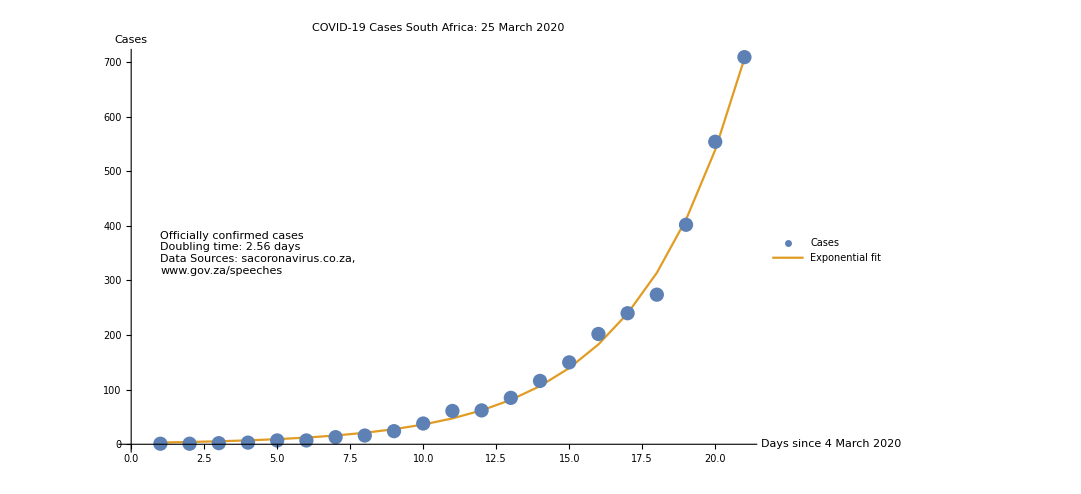

```mathematica
exportgraphic =Show[
ListPlot[{tdata["Values"], Table[eqn /. model, {x, 1,  Length[tdata["Values"]]}]}
, AxesLabel->{"Days since 4 March 2020", "Cases"}
, AxesStyle->Directive[Black, Bold, Medium]
, PlotLabel-> Style["COVID-19 Cases\nSouth Africa: "<>DateString[{"Day", " ", "MonthName", " ", "Year"}], Bold,Large]
, PlotTheme->"Default"
, Joined->{False, True}
, PlotLegends->{"Cases","Exponential fit"}
]
, Graphics[Style[Text["Officially confirmed cases\n"
<>"Doubling time: "<>ToString[NumberForm[First[d /. double], 3]]<>" days\n"
<>"Data Sources: sacoronavirus.co.za, \nwww.gov.za/speeches"
, {1,350}, {-1,0} ], Medium]]
, ImageSize->800

]
```

```mathematica
DateString[
```

```mathematica
exportfile =DateString[{"C:\\Users\\fskdm\\Projects\\2020_03_21_COV-19_Modeling\\","Year", "_", "Month", "_", "Day", "_FB.png"}];
CopyToClipboard[exportfile]
Export[exportfile,exportgraphic]
```

C:\Users\fskdm\Projects\2020_03_21_COV-19_Modeling\2020_03_25_FB.png

```mathematica
Reduce[( eqn /. model~Join~{x-> 6} )== 2 (eqn /. model), x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&x==3.48247 (1.02977+(0.+6.28319 ⅈ) C[1])

```mathematica
( eqn /. model )== 2 (eqn /. model)
```

2.04679 ⅇ^(0.287152 x)==4.09358 ⅇ^(0.287152 x)

```mathematica
( eqn /. model~Join~{x-> 2} )== 2 (eqn /. model)
```

3.63488==4.09358 ⅇ^(0.287152 x)

```mathematica
((eqn /. model)/.x-> (60))*2
```

2.4533×10^7

```mathematica
(eqn /. model)/.x-> (60+d)/.double
```

{2.4533×10^7}

```mathematica
double =Solve[((eqn /. model)/.x-> (60))*2 ==(eqn /. model)/.x-> (60+d), d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→2.56446}}

```mathematica
Log[eqn]//Simplify
```

Log[a ⅇ^(b x)]

```mathematica
Log[2.]/Log[200]*16.
```

2.09318

```mathematica
0.6931471805599453
```

```mathematica
12815/60.
```

213.583